```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-10-28"}];
laptop=FileNameJoin[{"/","home","karl"}];
labComp=FileNameJoin[{"C:","Users","kahrendsen2"}];
dropboxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns","18-01-03_PolarizingElectrons"}];
folder=FileNameJoin[{labComp,dropboxOn}];
SetDirectory[folder];
files=FileNames["*.dat"]
SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large];

plotLabel="Plot Label";
yAxisLabel="Y";
xAxisLabel="X";
ps={LabelStyle->18,PlotLabel->plotLabel,AxesLabel->{xAxisLabel,yAxisLabel}}
```

{EX2018-01-03_112039.dat,EX2018-01-03_113754.dat,EX2018-01-03_114402.dat,part1PumpScan.dat,part2PumpScan.dat}

{LabelStyle→18,PlotLabel→Plot Label,AxesLabel→{X,Y}}

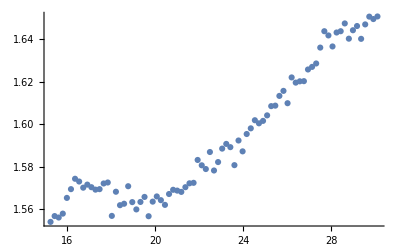

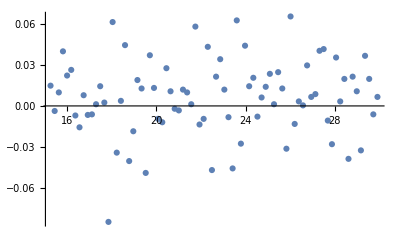

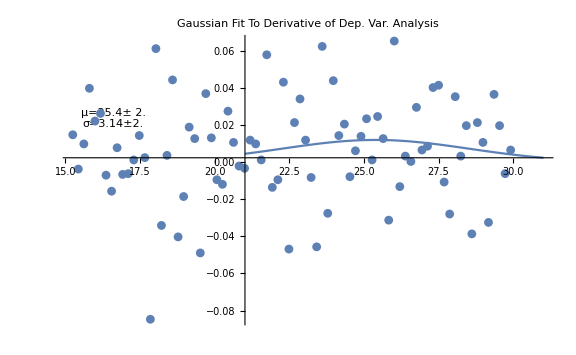

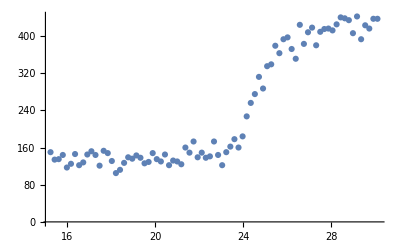

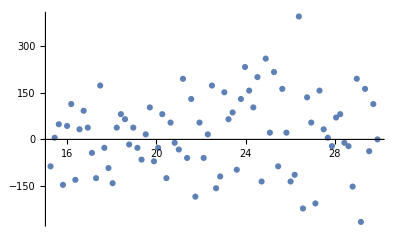

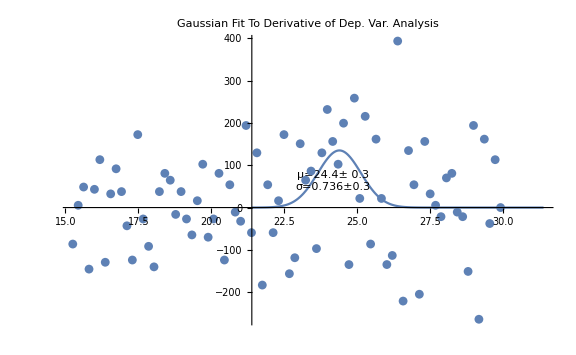

```mathematica
ExcitationFunctionProcessor["113754"]
```

```mathematica
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];


headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];

GaussianAnalyzer[timeString_,dependentVariableString_]:=Module[{file,ps,header,data,energy,energyDiff,depVar,depVarDiff,energyOneRemoved,depVarDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,dataLabel1,dataLabel2,x1,y1},
file=FileNames["*"<>ToString[timeString]<>".dat"][[1]];

header=GetFileHeaderInfo[file];
data=GetFileDataset[file];
energy=Reverse[Normal[data[All,"PrimaryElectronEnergy"]]];
depVar=Reverse[Normal[data[All,dependentVariableString]]];
depVarDiff=Differences[depVar];
energyDiff=Differences[energy];
energyOneRemoved=Take[energy,{1,-2}];
depVarDer=depVarDiff/energyDiff;
Print[ListPlot[Transpose[{energy,depVar}]]];
Print[ListPlot[Transpose[{energyOneRemoved,depVarDer}]]];


plotTitle="Gaussian Analysis";

plotData=Transpose[{energy,depVar}];
plotData2=Transpose[{energyOneRemoved,depVarDer}];


(*
yAxisTitle="d(Counts)/d(Energy)";
xAxisTitle="Electron Energy (eV)";
*)
dataLabel1="Data";
dataLabel2="Derivative";

ps={ImageSize->Large, PlotLabel->plotTitle,AxesLabel->{"X","Y"}};

plotData=plotData2;
gaussModel[x_]=ampl Evaluate[PDF[NormalDistribution[m,σ],x]];
(*Find the position of the peak of the derivative data*)
maxDerPos=Position[depVarDer,Max[depVarDer]][[1]];
energyOfPeak=energyOneRemoved[[maxDerPos]][[1]];

fit=NonlinearModelFit[plotData,gaussModel[x],{ampl,{m,energyOfPeak},σ},x];
model=Normal[fit];
pe=fit["BestFitParameters"]; (*Parameter Estimates*)
errors=fit["ParameterErrors"];


x1=energyOfPeak-(3σ/.pe);
y1=.25*(ampl)/.pe;
fitInfo=StringForm["μ=``± ``\nσ=``±``",NumberForm[m/.pe,3],NumberForm[errors[[2]],1],NumberForm[σ/.pe,3],NumberForm[errors[[3]],1]];
Print[Show[{Plot[gaussModel[x]/.pe,{x,energyOfPeak-5,energyOfPeak+5},PlotRange->All,PlotLabel->"Gaussian Fit To Derivative\nof Dep. Var. Analysis"],
Graphics[Text[fitInfo,{x1,y1}],BaseStyle->15],
ListPlot[plotData,PlotLabel->"PLOT2"]}]];
bothPlot=ListPlot[{Legended[plotData,dataLabel2],Legended[plotData2,dataLabel1]}];
derivativePlot=ListPlot[Legended[data2,dataLabel2],ps];

entry ={header["#Filename:"],header["#CVGauge(N2)(Torr):"],data[1,"N2Offset"],data[1,"bias"],m/.pe, σ/.pe,depVar[[1]],depVar[[-1]]}
];

ExcitationFunctionProcessor[timeString_]:=Module[{file,ps,header,data,energy,energyDiff,current,currentDiff,energyOneRemoved,currentDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,x1,y1},
GaussianAnalyzer[timeString,"Current"];
GaussianAnalyzer[timeString,"Count"];
];
```

```mathematica
file=FileNames["*"<>ToString[113754]<>".dat"][[1]];

header=GetFileHeaderInfo[file];
data=GetFileDataset[file]
belowThreshold=Normal[data[Select[#PrimaryElectronEnergy < 24.4-3*.7&],"Count"]]
averageBelowThreshold=N[Mean[belowThreshold]]
stdDevBelowThreshold=N[MeanDeviation[belowThreshold]]
```

Dataset[<>]

{149,139,173,149,160,124,130,132,122,145,130,135,148,129,126,138,143,136,139,127,112,105,131,148,153,121,144,152,145,128,122,146,125,117,144,135,134,150}

136.474

10.9723